```mathematica
T[x_,y_,t_]:=CT Tt[t]Sin[(π x)/Lx]Sin[(π y)/Ly];
phi[x_,y_,t_]:=CF PHIt[t] Sin[(π x)/Lx]Sin[(π y)/Ly] x/Lx y/Ly;
```

```mathematica
xsrem[T_]:=xsaref+doppler (√T-√Tref);
k[T_]:=k0+k1 (T-Tref);
```

```mathematica
{{D[T[x,y,t],x],D[T[x,y,t],y]},{D[phi[x,y,t],x],D[phi[x,y,t],y]}}//MatrixForm
```

((CT π Cos[(π x)/Lx] Sin[(π y)/Ly] Tt[t])/Lx | (CT π Cos[(π y)/Ly] Sin[(π x)/Lx] Tt[t])/Ly
(CF π x y Cos[(π x)/Lx] PHIt[t] Sin[(π y)/Ly])/(Lx^2 Ly)+(CF y PHIt[t] Sin[(π x)/Lx] Sin[(π y)/Ly])/(Lx Ly) | (CF π x y Cos[(π y)/Ly] PHIt[t] Sin[(π x)/Lx])/(Lx Ly^2)+(CF x PHIt[t] Sin[(π x)/Lx] Sin[(π y)/Ly])/(Lx Ly))

```mathematica
qT[xx_,yy_,tt_]:=(rho cp D[T[x,y,t], t]-k[T[x,y,t]] (D[T[x,y,t], x,x]+D[T[x,y,t], y,y])-kappa xsfiss phi[x,y,t])/.{x->xx,y->yy,t->tt};
qF[xx_,yy_,tt_]:=(invvel D[phi[x,y,t], t]-xsdiff (D[phi[x,y,t], x,x]+D[phi[x,y,t], y,y])-(nu xsfiss -xsrem[T[x,y,t]]) phi[x,y,t])/.{x->xx,y->yy,t->tt};
```

```mathematica
Tt[t_]:=1+Tanh[rT t];
PHIt[t_]:=1+Exp[rF t];
```

```mathematica
CT=1;
CF=1;
rT=1;
rF=0.25;
Lx=100;
Ly=100;
invvel=2 10^-4;
xsdiff=1.268;
xsfiss=0.00191244;
xsaref=0.0349778;
doppler=1 10^-5;
nu=2.41;
kappa=1 10^-11;
rho=1;
cp=1;
k0=3 10^-3;
k1=2 10^-4;
Tref=0;
```

```mathematica
Manipulate[
GraphicsGrid[{
{Plot3D[T[x,y,tt],{x,0,Lx},{y,0,Ly}],Plot3D[phi[x,y,tt],{x,0,Lx},{y,0,Ly}]},
{Plot3D[qT[xx,yy,tt],{xx,0,Lx},{yy,0,Ly}],Plot3D[qF[xx,yy,tt],{xx,0,Lx},{yy,0,Ly}]}
}],{tt,0,4,0.1}
]
```

```mathematica
qT[x,y,t]/.{Tt'[t]->dTdt,Tt[t]->Tt,PHIt[t]->PHIt}//CForm
```

dTdt*Sin((Pi*x)/100.)*Sin((Pi*y)/100.) - 1.91244e-18*PHIt*x*y*Sin((Pi*x)/100.)*Sin((Pi*y)/100.) + 
   (Power(Pi,2)*Tt*Sin((Pi*x)/100.)*Sin((Pi*y)/100.)*(0.003 + (Tt*Sin((Pi*x)/100.)*Sin((Pi*y)/100.))/5000.))/5000.

```mathematica
qF[x,y,t]/.{PHIt'[t]->dPHIdt,Tt[t]->Tt,PHIt[t]->PHIt}//CForm
```

5.e-9*Power(E,0.25*t)*x*y*Sin((Pi*x)/100.)*Sin((Pi*y)/100.) - 
   1.268*((PHIt*Pi*x*Cos((Pi*y)/100.)*Sin((Pi*x)/100.))/500000. + (PHIt*Pi*y*Cos((Pi*x)/100.)*Sin((Pi*y)/100.))/500000. - 
      (PHIt*Power(Pi,2)*x*y*Sin((Pi*x)/100.)*Sin((Pi*y)/100.))/5.e7) - 
   (PHIt*x*y*Sin((Pi*x)/100.)*Sin((Pi*y)/100.)*(-0.030368819600000003 - Sqrt(Tt*Sin((Pi*x)/100.)*Sin((Pi*y)/100.))/100000.))/10000.

```mathematica
phiCL=Flatten[Table[Chop[phi[x,x,3]],{x,0,Lx,0.05}]];
TCL=Flatten[Table[Chop[T[x,x,3]],{x,0,Lx,0.05}]];
```

```mathematica
THerm=Flatten[Import["TCL.dat"]];
PhiHerm=Flatten[Import["PhiCL.dat"]];
```

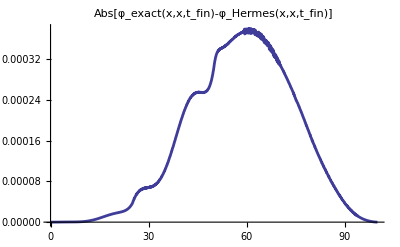

```mathematica
ListLinePlot[MapThread[Subtract,{phiCL[[1;;2000]],PhiHerm[[1;;2000]]}],PlotLabel->Style[Abs[Subscript[φ, exact][x,x,Subscript[t, fin]]-Subscript[φ, Hermes][x,x,Subscript[t, fin]]],FontSize->28], AxesLabel->{x},Ticks->{Table[{20 i,i},{i,0,100,10}],Automatic}, PlotStyle->Thickness[0.005],AxesStyle->Directive[FontSize->22,Thickness[0.004]],ImageSize->Scaled[0.75]]
```

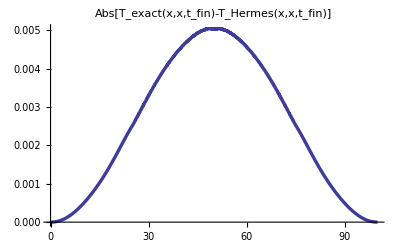

```mathematica
ListLinePlot[Map[Abs,MapThread[Subtract,{TCL[[1;;2000]],THerm[[1;;2000]]}]],PlotLabel->Style[Abs[Subscript[T, exact][x,x,Subscript[t, fin]]-Subscript[T, Hermes][x,x,Subscript[t, fin]]],FontSize->28], AxesLabel->{x},Ticks->{Table[{20 i,i},{i,0,100,10}],Automatic}, PlotStyle->Thickness[0.006],AxesStyle->Directive[FontSize->22,Thickness[0.004]],ImageSize->Scaled[0.75]]
```